```mathematica
一些方向的磁场分布
```

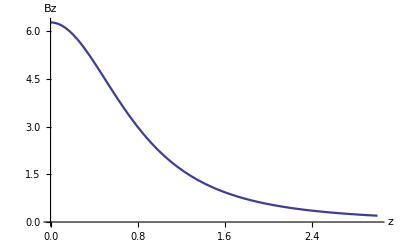

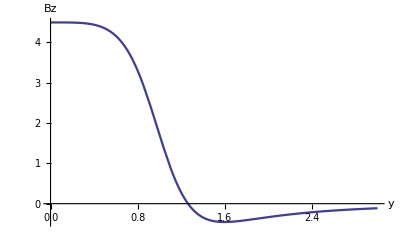

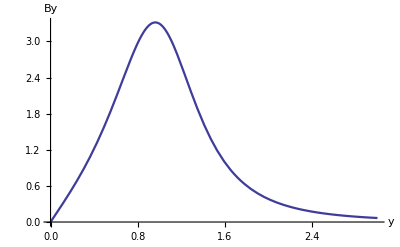

-Graphics3D-

```mathematica
By[y_,z_]:=
NIntegrate[(R*z*Sin[φ])/((y^2+z^2+R^2-2y*R*Sin[φ])^(3/2)),
{φ,0,2π}];
Bz[y_,z_]:=
NIntegrate[(R*(R-y*Sin[φ]))/((y^2+z^2+R^2-2y*R*Sin[φ])^(3/2)),
{φ,0,2π}];R=1.;
Plot[Bz[0,z],{z,0,3R},AxesLabel->{"z","Bz"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[Bz[y,R/2],{y,0,3R},AxesLabel->{"y","Bz"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[By[y,R/2],{y,0,3R},AxesLabel->{"y","By"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot3D[Bz[y,z],{y,-3R,3R},{z,-3R,3R},
PlotRange->All,PlotPoints->50,Mesh->False,
AxesLabel->{"y","z","Bz"},
AxesStyle->Thickness[0.003]]
Clear[R,Bz,By]
```